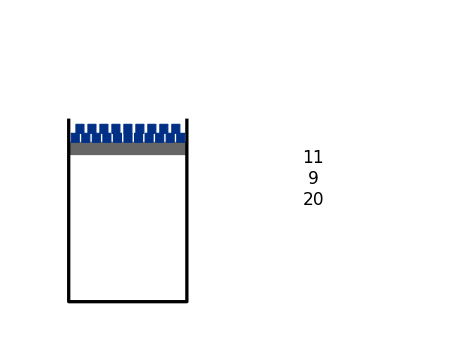

```mathematica
Module[{h1,h2,height,δ1,L1,δ2,row1,row2,j},

h1=0.9;
h2=h1+0.075;

(*height=0.055;
δ1=0.01501;
L1=0.05325;
δ2=0.01501;*)
height=0.055;
δ1=0.015;
L1=0.0475;
δ2=0.0235;
(*j=0.25;*)

row1=Table[Rectangle[{n*δ1+(n-1)*L1,h2},{n*δ1+n*L1,h2+height}],{n,1,11}];
row2=Table[Rectangle[{0.25*(2*δ1+L1)+n*δ2+(n-1)*L1,h2+height},{0.25*(2*δ1+L1)+n*δ2+n*L1,h2+2*height}],{n,1,9}];
(*row2=Table[Rectangle[{0.5*((n+1)*δ1+n*L1),h2+height},{0.5*((n+1)*δ1+n*L1)+L1+δ2,h2+2*height}],{n,1,9}];*)
(*row1=Table[Rectangle[{n*δ1+(n-1)*L1,h2},{n*δ1+n*L1,h2+height}],{n,1,10}];*)
(*row2=Table[Rectangle[{n*δ2+(n-1)*L1,h2+height},{n*δ2+n*L1,h2+2*height}],{n,1,10}];*)
(*row2=Table[Rectangle[{n*δ1+(n-1)*L1,h2+height},{n*δ1+n*L1,h2+2*height}],{n,1,10}];*)
(*row3=Table[Rectangle[{n*δ1+(n-1)*L1,h2+2*height},{n*δ1+n*L1,h2+3*height}],{n,1,10}];*)

Framed@Graphics[{
{EdgeForm[Thick],GrayLevel[0.4],Rectangle[{0,h1},{0.7,h2}]},
{Thickness[0.005],Line[{{0,1.12},{0,0},{0.7,0},{0.7,1.12}}],(*Line[{{1.25,1.12},{1.25,0},{1.95,0},{1.95,1.12}}]*)},
{EdgeForm[Thick],RGBColor[0.,0.19,0.52],row1,row2},
Text[Style[Column[{Length[row1],Length[row2],Length[row1]+Length[row2]}],17],{1.45,0.75}],
},ImageSize->{475,350},PlotRange->{{-0.15,2.15},{-0.1,1.65}}]
]
```